## Superposition and Entanglement

```mathematica
<<Wolfram`QuantumFramework`
```

### Key Concepts

Superposition

Entanglement

GHZ state

Partial Trace

Mixed State

Pure State

### Superposition and Entanglement

Quantum superposition and quantum entanglement are terms you may have heard often in popular culture.

A superposition is simply a quantum state which is not in any state in the measurement basis. Instead, it is in a linear combination of more than one basis state. You have seen many such states represented as vectors.

A uniform superposition has equal chance to give each basis state when measured:

```mathematica
QuantumState["UniformSuperposition"]["Formula"]
```

1/(√2)0+1/(√2)1

Consider the 2-qubit uniform superposition state:

```mathematica
QuantumState["UniformSuperposition"[2]]["Formula"]
```

1/2 00+1/2 01+1/2 10+1/2 11

This state is equivalent to each of the single qubits being in a uniform superposition as well:

```mathematica
nonentangled=QuantumTensorProduct[QuantumState["UniformSuperposition"],QuantumState["UniformSuperposition"]]
```

QuantumState[…]

```mathematica
nonentangled==QuantumState["UniformSuperposition"[2]]
```

True

```mathematica
nonentangled["Formula"]
```

1/2 00+1/2 01+1/2 10+1/2 11

Since each qubit in this state can be represented as its own independent state (by the tensor product construction), there is no entanglement present in this state.

```mathematica
QuantumEntangledQ[nonentangled]
```

False

Entanglement describes a quantum system in which parts of that system cannot be given complete, independent descriptions. In other words, the whole system has a definite state, but some individual parts may not have a definite state.

This may sound exotic, however it is relatively straightforward to create entangled quantum states. Consider the following circuit:

```mathematica
sameEntangler=QuantumCircuitOperator[{"H"->1,"CNOT"->{1,2}}]
```

QuantumCircuitOperator[…]

When applied to the register state, this circuit will create the famous Bell state:

```mathematica
entangled=sameEntangler[]
```

QuantumState[…]

```mathematica
entangled==QuantumState["Bell"]
```

True

```mathematica
entangled["Formula"]
```

1/(√2)00+1/(√2)11

Unlike the tensor product state leading to a uniform superposition, the only possible measurement outcomes for this state are “00” or “11”.

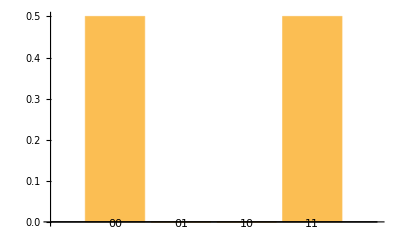

```mathematica
entangled["ProbabilitiesPlot"]
```

Before measuring the Bell state, what can you say about the individual qubit states? In some sense, you might be able to say that each qubit is in “the same” state. But what is that state? Until it is measured, you don’t know if they are both “0” or both “1”. But you do know the results will be identical when measuring each qubit in this state.

This certainty about measurement correlations that still leave the individual states in question is the hallmark of entanglement.

```mathematica
QuantumEntangledQ[entangled]
```

True

The following circuit also creates entanglement, but this time the results of each qubit are opposites:

```mathematica
oppositeEntangler=QuantumCircuitOperator[{"H"->1,"C0NOT"->{1,2}}]
```

QuantumCircuitOperator[…]

Apply the circuit:

```mathematica
entangled2=oppositeEntangler[]
```

QuantumState[…]

Check for entanglement:

```mathematica
QuantumEntangledQ[entangled2]
```

True

Visualize the results:

```mathematica
entangled2["Formula"]
```

1/(√2)01+1/(√2)10

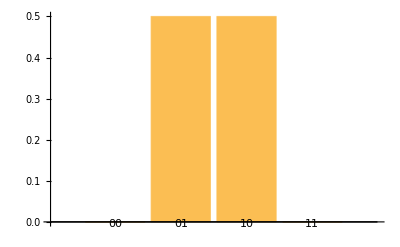

```mathematica
entangled2["ProbabilitiesPlot"]
```

### GHZ States

Entanglement can extend beyond only two qubits. The GHZ circuit is shown below:

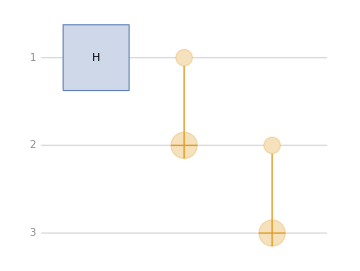

```mathematica
QuantumCircuitOperator["GHZ"]["Diagram"]
```

This circuit creates a state in which the measurement of all qubits will be perfectly correlated, but you can’t tell the result before measuring:

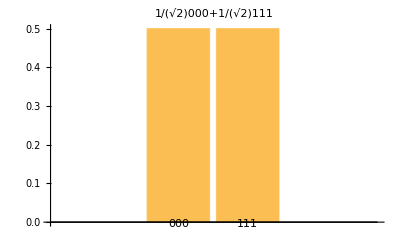

```mathematica
QuantumState["GHZ"]["ProbabilityPlot",PlotLabel->Highlighted[QuantumState["GHZ"],Background->LightBlue]]
```

In this case, all three qubits share in the entanglement:

```mathematica
QuantumEntangledQ[QuantumState["GHZ"]]
```

True

Such a state is called a GHZ state. The GHZ type states can be extended to any number of qubits:

```mathematica
QuantumState["GHZ"[5]]["Formula"]
```

1/(√2)00000+1/(√2)11111

### Partial Traces

Earlier in the lesson, you may have wondered what can be said about a qubit which is entangled with other qubits. Surely it must be possible to assign some kind of state to that qubit. Subsystems of a larger quantum system can be assigned states through the mathematical operation known as a partial trace.

Let’s start with the non-entangled 2-qubit state from before and “trace out” the second qubit. The result will be some kind of state for the first qubit. This can be done using QuantumPartialTrace:

```mathematica
singleNoEntanglement=QuantumPartialTrace[nonentangled,{2}]
```

QuantumState[…]

The result is a quantum state. This state is the same as the uniform superposition:

```mathematica
singleNoEntanglement==QuantumState["UniformSuperposition"]
```

True

```mathematica
singleNoEntanglement["Formula"]//TraditionalForm
```

1/(√2)0+1/(√2)1

That result should be expected since the non-entangled state was a tensor product state by construction.

But what happens if we try the same procedure with the entangled state?

```mathematica
singleEntanglement=QuantumPartialTrace[entangled,{2}]
```

QuantumState[…]

The result is no longer simply the uniform superposition state:

```mathematica
singleEntanglement==QuantumState["UniformSuperposition"]
```

False

In fact, it is a type of state which has not appeared in this course previously.

```mathematica
singleEntanglement//TraditionalForm
```

1/2 00+1/2 11

This formula appears strange, because a single qubit from a bell pair must be described by what is known as a mixed state.

```mathematica
singleEntanglement["MixedStateQ"]
```

True

This is in contrast with states known as pure states:

```mathematica
singleNoEntanglement["PureStateQ"]
```

True

The difference is subtle. A pure state can be represented by a state vector, which means a pure state is a definite linear combination of basis vectors. Depending on your measurement basis, you may not get the same result every time; however, linear algebra results guarantee there will be some measurement basis in which you can get the same result every time.

In contrast, a subsystem in a mixed state has inherent uncertainty built into the subsystem. You cannot find a measurement basis for the subsystem alone which will guarantee the same result every time. That’s because entanglement implies that the subsystem shares information with some larger system.

For example, the Bell pair of qubits share the information that they will either both give “0” or both give “1”. However, there is an equal chance of either result, giving some inherent uncertainty about the single qubit states.

The mixed single-qubit has 1 bit of entropy:

```mathematica
singleEntanglement["Entropy"]
```

1 b

The pure single-qubit has 0 bits of entropy:

```mathematica
singleNoEntanglement["Entropy"]
```

0 b

The mixed-state single qubit can be “purified” by considering it as part of a larger system:

```mathematica
singleEntanglement["Purify"]
```

QuantumState[…]

It should not surprise you that the larger, purified state is none other than the Bell state you started with:

```mathematica
singleEntanglement["Purify"]==entangled==QuantumState["Bell"]
```

True

Even though the mixed and pure single-qubit states differ in this very important property, the probability distributions for the single qubit are identical:

```mathematica
singleEntanglement["Probabilities"]==singleNoEntanglement["Probabilities"]
```

True

It is only by measuring the full system (the first and second qubits in this case) that entanglement can be seen in the correlations:

```mathematica
entangled["Probabilities"]==nonentangled["Probabilities"]
```

False

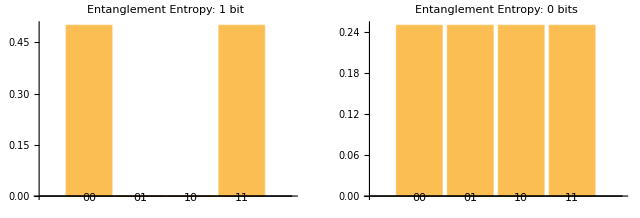

```mathematica
GraphicsRow[Map[#["ProbabilitiesPlot",PlotLabel->("Entanglement Entropy: "<>ToString@QuantumEntanglementMonotone[#,"EntanglementEntropy"])]&,{entangled,nonentangled}],Frame->All]
```

You can also see the difference between mixed and pure single-qubit states from their Bloch plots:

```mathematica
singleNoEntanglement["BlochPlot"]
```

-Graphics3D-

The pure state is just the 𝓍_+ eigenstate:

```mathematica
singleNoEntanglement==QuantumState["+"]
```

True

In contrast, this mixed state is precisely in the middle of the Bloch sphere:

```mathematica
singleEntanglement["BlochSphericalCoordinates"]
```

{0,0,0}

```mathematica
singleEntanglement["BlochPlot"]
```

-Graphics3D-

No matter which basis you choose to measure this qubit, you are guaranteed uncertainty. Such a state is known as a uniform mixture:

```mathematica
singleEntanglement==QuantumState["UniformMixture"]
```

True